## Вариант 9 Задание 4

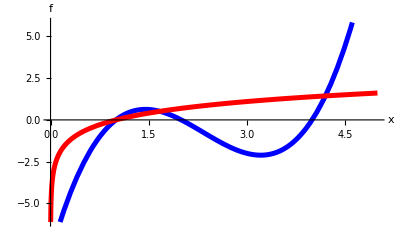

```mathematica
Plot[{x^3-7 x^2+14x-8,Log[E,x]},{x,0,5}, PlotStyle->{{Thickness[0.009],RGBColor[0,0,1]}, {Thickness[0.009],RGBColor[1,0,0]}}, AxesLabel->{"x","f"}]                                  (*Находим приближенные значения корней построив графики левой и правой частей уравнения*)
```

```mathematica
x1=1; x2=1.65; x3=4.2;
```

```mathematica
FindRoot[x^3-7 x^2+14x-8==Log[E,x],{x,x1}] (*находим точные значения корней*)
FindRoot[x^3-7 x^2+14x-8==Log[E,x],{x,x2}]
FindRoot[x^3-7 x^2+14x-8==Log[E,x],{x,x3}]
```

{x→1.}

{x→1.67145}

{x→4.20343}

## Задание 5

```mathematica
sol1 = NDSolve[{y''[x]+x^2 y'[x]+3 Cos[x]^2 y[x]==0,y[0]==1,y'[0]==-1},y,{x,-2,4}]
```

{{y→InterpolatingFunction[…]}}

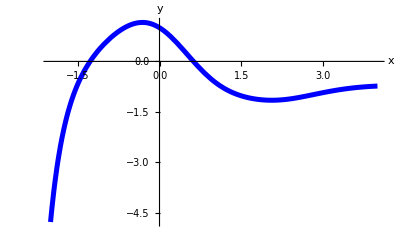

```mathematica
Plot[y[x]/.sol1,{x,-2,4},AxesLabel->{"x","y"},PlotStyle->{RGBColor[0,0,1],Thickness[0.009]}]
```

```mathematica
sol2=FindRoot[(y[x]/.sol1[[1]])==0,{x,0.6}]                           (*Первый корень приблизительно равен 0.6*)
```

{x→0.622733}

```mathematica
sol3=FindRoot[(y[x]/.sol1[[1]])==0,{x,-1.25}]                       (*Второй корень приблизительно равен -1.25*)
```

{x→-1.27396}

```mathematica
D[y[x]/.sol1[[1]],x]/.sol2                                                                      (*Производная в точке ~0.6*)
```

-1.80514

```mathematica
D[y[x]/.sol1[[1]],x]/.sol3                                                                       (*Производная в точке ~-1.25*)
```

2.40723

```mathematica
sol4=FindRoot[D[y[x]/.sol1[[1]],x]==0,{x,2}]                         (*Локальный минимум около точки 2. Находим точное значение x приравнивая производную функции к нулю*)
```

{x→2.06021}

```mathematica
y[x]/.sol1[[1]]/.sol4
```

-1.15305

```mathematica
FindMinimum[y[x]/.sol1[[1]],{x,2}]                                                        (*Минимальное значение функции в точке x*)
```

{-1.15305,{x→2.06021}}

## Задание 6

```mathematica
dat1=Table[{x,(1+2x+3 x^2+4 x^3+5 x^4)(1+Random[Real,{-0.1,0.1}])},{x,0,4,0.2}]
```

{{0.,0.955512},{0.2,1.44709},{0.4,2.53295},{0.6,4.55945},{0.8,9.27893},{1.,14.5053},{1.2,25.123},{1.4,38.8425},{1.6,64.9621},{1.8,97.501},{2.,132.097},{2.2,172.26},{2.4,246.644},{2.6,315.157},{2.8,441.798},{3.,599.567},{3.2,723.849},{3.4,826.857},{3.6,1002.45},{3.8,1437.41},{4.,1558.01}}

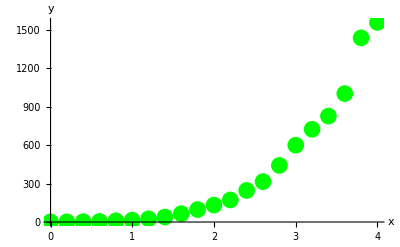

```mathematica
p1=ListPlot[dat1,PlotStyle->{PointSize[0.03],RGBColor[0,1,0]},AxesLabel->{"x","y"}]
```

```mathematica
y1=Fit[dat1,{1,x,x^2,x^3,x^4},x]
```

0.799848+4.30016 x-2.18888 x^2+7.59875 x^3+4.40111 x^4

```mathematica
y2=Fit[dat1,{1,x,Sin[x],Cos[x],Sin[2x],Cos[2x]},x]
```

-586.559+599.089 x+610.731 Cos[x]-31.9822 Cos[2 x]-328.921 Sin[x]-76.1662 Sin[2 x]

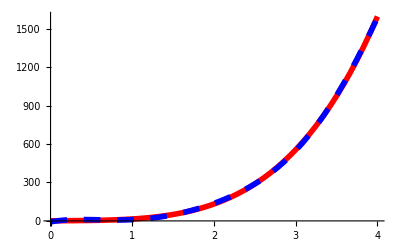

```mathematica
p2=Plot[{y1,y2},{x,0,4},PlotStyle->{{Thickness[0.01],RGBColor[1,0,0]},{Thickness[0.01],RGBColor[0,0,1],Dashing[{0.03}]}}]
```

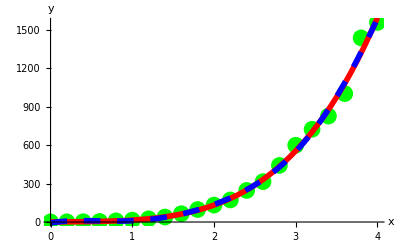

```mathematica
Show[p1,p2]
```

```mathematica
dat2=Table[{x,(1+2x+3Sin[x]+4Cos[x])(1+Random[Real,{-0.1,0.1}])},{x,0,4,0.2}]
```

{{0.,5.17874},{0.2,6.02988},{0.4,6.88641},{0.6,6.63781},{0.8,7.60018},{1.,7.44273},{1.2,7.52086},{1.4,7.03155},{1.6,6.66486},{1.8,7.03248},{2.,5.51345},{2.2,5.36855},{2.4,4.67881},{2.6,4.05753},{2.8,4.02939},{3.,3.71083},{3.2,3.52416},{3.4,3.168},{3.6,3.46378},{3.8,3.34007},{4.,4.27035}}

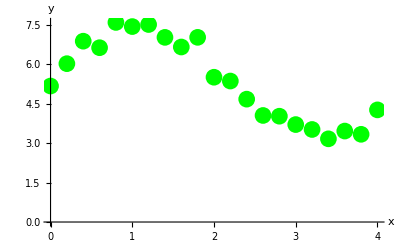

```mathematica
p3=ListPlot[dat2,PlotStyle->{PointSize[0.03],RGBColor[0,1,0]},AxesLabel->{"x","y"}]
```

```mathematica
y3=Fit[dat2,{1,x,Sin[x],Cos[x]},x]
```

1.63339+1.70009 x+3.59716 Cos[x]+2.59328 Sin[x]

```mathematica
y4=Fit[dat2,{1,x,x^2,x^3,x^4},x]
```

5.13751+5.17226 x-3.27304 x^2+0.393082 x^3+0.0217021 x^4

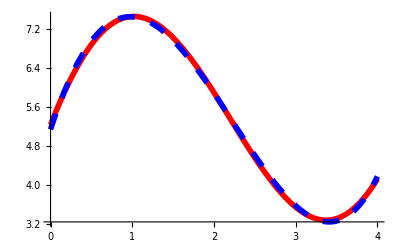

```mathematica
p4=Plot[{y3,y4},{x,0,4},PlotStyle->{{Thickness[0.01],RGBColor[1,0,0]},{Thickness[0.01],RGBColor[0,0,1],Dashing[{0.03}]}}]
```

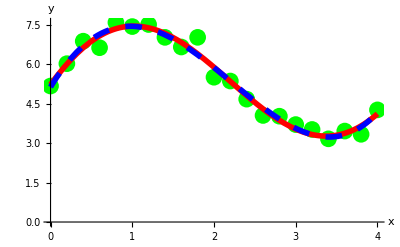

```mathematica
Show[p3,p4]
```